```mathematica
Quit[]
```

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

# Loop Contribution

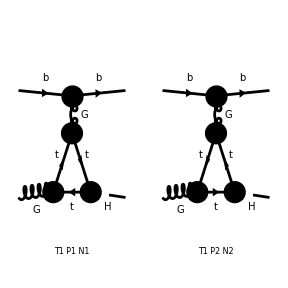

FeynArtsGraphics({b,G}→{b,H})(([T1 P1 N1] | [T1 P2 N2] | Null
Null | Null | Null
Null | Null | Null))

```mathematica
diagloop=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies,AllBoxes}],{F[12],V[4]}->{F[12],S[1]},InsertionLevel->{Particles},Model->{"htt"},GenericModel->{"htt"},LastSelections->{V[4],F[9]}];
Paint[diagloop]
```

```mathematica
amploop=FCFAConvert[CreateFeynAmp[diagloop,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]},LoopMomenta->{l},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->4]/.M$FACouplings/.{FAGS->gs,ybcky->yt,FCGV["MT"]->MT};
```

```mathematica
amploop=Plus@@amploop/.{DiracTrace->TR}//SUNSimplify//ChangeDimension[#,D]&//TID[#,l,ToPaVe->True]&//ChangeDimension[#,4]&//ReplaceAll[#,{D->4}]&//Simplify;
```

```mathematica
FCClearScalarProducts[]
SetMandelstam[s,t,u,p[1],p[2],-p[3],-p[4],MB,0,MB,MH];
amploop=amploop//Simplify;
```

```mathematica
Cases[amploop,_B0,Infinity]//DeleteDuplicates//StandardForm
```

{B0[MH^2,MT^2,MT^2],B0[t,MT^2,MT^2],B0[0,MT^2,MT^2]}

```mathematica
beta=Sqrt[4 MT^2/MH^2-1];
beta1=Sqrt[1-4 MT^2/t];
scalarIntegral={_C0->(1/2/(t-MH^2) (Log[(beta1+1)/(beta1-1)]^2+ ArcTan[2 beta/(1-beta^2)]^2)),
B0[MH^2,MT^2,MT^2]->(1/ep+Log[m^2/MH^2]+2-beta ArcTan[2 beta/(beta^2-1)]-Log[(1+beta^2)/4]),
B0[t,MT^2,MT^2]->(1/ep+Log[m^2/(-t)]+2+beta1 Log[beta1-1]-beta1 Log[beta1+1]-Log[(beta1^2-1)/4]),
B0[0,MT^2,MT^2]->(1/ep+Log[m^2/MT^2])};
```

```mathematica
amploop=Series[amploop/.scalarIntegral,{ep,0,0}]//Simplify//PropagatorDenominatorExplicit//Normal;
```

# Tree Contributions

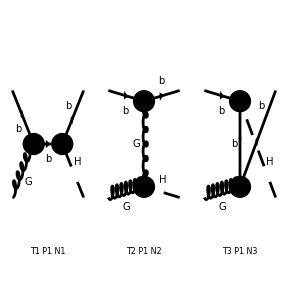

FeynArtsGraphics({b,G}→{b,H})(([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
Null | Null | Null
Null | Null | Null))

```mathematica
diagtree=InsertFields[CreateTopologies[0,2->2],{F[12],V[4]}->{F[12],S[1]},InsertionLevel->{Particles},Model->{"hbb"},GenericModel->{"hbb"}];
Paint[diagtree]
```

```mathematica
amptree=FCFAConvert[CreateFeynAmp[diagtree,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3],p[4]},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->4]/.M$FACouplings/.{FAGS->gs,ybcky->yb,al->be,FCGV["MB"]->MB};
```

```mathematica
amptree=amptree[[1]]+amptree[[3]]//Contract//PropagatorDenominatorExplicit//Simplify;
```

```mathematica
amptree
```

((s-MB^2) (ⅈ gs (γ̄)^Lor1 T_Col3Col1^Glu2).(γ̄·(OverBar[p(3)]-OverBar[p(2)])+MB).(yb (((γ̄)^6-(γ̄)^7) sin(be)-ⅈ ((γ̄)^6+(γ̄)^7) cos(be)))/(√2)+(u-MB^2) (yb (((γ̄)^6-(γ̄)^7) sin(be)-ⅈ ((γ̄)^6+(γ̄)^7) cos(be)))/(√2).(γ̄·(OverBar[p(3)]+OverBar[p(4)])+MB).(ⅈ gs (γ̄)^Lor1 T_Col3Col1^Glu2))/((MB^2-s) (MB^2-u))

# Square

```mathematica
spinsum[p_,h_]:=1/4 (1+h GA[5]).(GS[p]+MB).(1-h GA[5]);
```

```mathematica
ampsum=amploop+amptree;
ampS=MT[Lor1,Lor2]spinsum[p[3],hf].ampsum.spinsum[p[1],hi].(ComplexConjugate[ampsum]/.{Lor1->Lor2,Lor3->Lor4})//PropagatorDenominatorExplicit//Contract//Simplify;
```

```mathematica
ampS
```

1/16 (hf (γ̄)^5+1).(MB+γ̄·OverBar[p(3)]).(1-hf (γ̄)^5).1/(8 √2)gs (-1/(π^2 (MH^2-t)^3 t)MT yt (2 B_0(MH^2,MT^2,MT^2) cos(al) (t (γ̄)^Lor2 (MH^2-t)^2+2 (-2 MH^4+t MH^2+t^2) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+2 γ̄·OverBar[p(2)] (2 (MH^4+2 t MH^2) OverBar[p(2)]^Lor2+t (t-MH^2) OverBar[p(4)]^Lor2))-2 B_0(t,MT^2,MT^2) cos(al) (t (γ̄)^Lor2 (MH^2-t)^2-2 (MH^4+t MH^2-2 t^2) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+2 γ̄·OverBar[p(2)] ((MH^4+4 t MH^2+t^2) OverBar[p(2)]^Lor2+t (t-MH^2) OverBar[p(4)]^Lor2))-(MH^2-t) (4 B_0(0,MT^2,MT^2) cos(al) ((MH^2+t) γ̄·OverBar[p(2)]+(t-MH^2) γ̄·OverBar[p(4)]) OverBar[p(2)]^Lor2+C_0(0,MH^2,t,MT^2,MT^2,MT^2) ((MH^2-4 MT^2-t) cos(al) (γ̄)^Lor2 (MH^2-t)^2+2 ((MH^2+4 MT^2+t) cos(al) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+(MH^2-t) (γ̄)^Lor3 ϵ^(Lor2Lor3 OverBar[p(2)]OverBar[p(4)]) sin(al)) (MH^2-t)-2 cos(al) γ̄·OverBar[p(2)] (4 (2 MT^2+t) OverBar[p(2)]^Lor2 MH^2+(MH^2-t) (MH^2-4 MT^2-t) OverBar[p(4)]^Lor2)))) gs^2-8 ⅈ yb (((γ̄)^Lor2.(MB+γ̄·(OverBar[p(3)]-OverBar[p(2)])).(((γ̄)^6-(γ̄)^7) sin(be)-ⅈ cos(be) ((γ̄)^6+(γ̄)^7)))/(MB^2-u)+((((γ̄)^6-(γ̄)^7) sin(be)-ⅈ cos(be) ((γ̄)^6+(γ̄)^7)).(MB+γ̄·(OverBar[p(3)]+OverBar[p(4)])).(γ̄)^Lor2)/(MB^2-s))) T_Col3Col1^Glu2.(hi (γ̄)^5+1).(MB+γ̄·OverBar[p(1)]).(1-hi (γ̄)^5).1/(8 √2)gs (8 ⅈ yb (((γ̄)^Lor2.(MB+γ̄·(OverBar[p(3)]+OverBar[p(4)])).(ⅈ cos(be) ((γ̄)^6+(γ̄)^7)+((γ̄)^7-(γ̄)^6) sin(be)))/(MB^2-s)+((ⅈ cos(be) ((γ̄)^6+(γ̄)^7)+((γ̄)^7-(γ̄)^6) sin(be)).(MB+γ̄·(OverBar[p(3)]-OverBar[p(2)])).(γ̄)^Lor2)/(MB^2-u))-1/(π^2 (MH^2-t)^3 t)gs^2 MT yt (2 B_0(MH^2,MT^2,MT^2) cos(al) (t (γ̄)^Lor2 (MH^2-t)^2+2 (-2 MH^4+t MH^2+t^2) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+2 γ̄·OverBar[p(2)] (2 (MH^4+2 t MH^2) OverBar[p(2)]^Lor2+t (t-MH^2) OverBar[p(4)]^Lor2))-2 B_0(t,MT^2,MT^2) cos(al) (t (γ̄)^Lor2 (MH^2-t)^2-2 (MH^4+t MH^2-2 t^2) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+2 γ̄·OverBar[p(2)] ((MH^4+4 t MH^2+t^2) OverBar[p(2)]^Lor2+t (t-MH^2) OverBar[p(4)]^Lor2))-(MH^2-t) (4 B_0(0,MT^2,MT^2) cos(al) ((MH^2+t) γ̄·OverBar[p(2)]+(t-MH^2) γ̄·OverBar[p(4)]) OverBar[p(2)]^Lor2+C_0(0,MH^2,t,MT^2,MT^2,MT^2) ((MH^2-4 MT^2-t) cos(al) (γ̄)^Lor2 (MH^2-t)^2+2 ((MH^2+4 MT^2+t) cos(al) γ̄·OverBar[p(4)] OverBar[p(2)]^Lor2+(MH^2-t) (γ̄)^Lor4 ϵ^(Lor2Lor4 OverBar[p(2)]OverBar[p(4)]) sin(al)) (MH^2-t)-2 cos(al) γ̄·OverBar[p(2)] (4 (2 MT^2+t) OverBar[p(2)]^Lor2 MH^2+(MH^2-t) (MH^2-4 MT^2-t) OverBar[p(4)]^Lor2))))) T_Col1Col3^Glu2

```mathematica
<<FeynCalcFormLink`
```

```mathematica
ampS=FeynCalcFormLink[DiracTrace[ampS]];
```

```mathematica
ampS1=ampS/.{al->0}//Contract//Simplify;
```

```mathematica
result=Series[ampS1/.scalarIntegral,{ep,0,0}]//Normal;
```

```mathematica
result
```

```mathematica
Clear[tmp];
tmp=Solve[e+Sqrt[e^2+MB^2]==Sqrt[e1^2+MB^2]+Sqrt[e1^2+MH^2],e1]//FullSimplify[#,MB>0 && MH>4 MB && e>0]&;
```

```mathematica
(*Kinematics*)
spd[x_,y_]:=x[[1]] y[[1]]-x[[2]] y[[2]]-x[[3]] y[[3]]-x[[4]] y[[4]];
eps[p[a_],p[b_],p[c_],p[d_]]:=Plus@@(q[a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,2,3,4},{1,3,4,2},{1,4,2,3},{2,1,4,3},{2,4,3,1},{2,3,1,4},{3,1,2,4},{3,2,4,1},{3,4,1,2},{4,1,3,2},{4,3,2,1},{4,2,1,3}})-Plus@@(q     [a][[#[[1]]]] q[b][[#[[2]]]] q[c][[#[[3]]]] q[d][[#[[4]]]]&/@{{1,3,2,4},{1,2,4,3},{1,4,3,2},{2,1,3,4},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,2,1},{3,2,1,4},{4,1,2,3},{4,2,3,1},{4,3,1,2}});
e1=e1/.tmp[[2]];
q[1]={Sqrt[e^2+MB^2],0,0,e};(*pbin*)
q[2]={e,0,0,-e};(*pgin*)
q[3]={Sqrt[e1^2+MB^2],e1 Sin[th],0,e1 Cos[th]};(*pbout*)
q[4]={Sqrt[e1^2+MH^2],-e1 Sin[th],0,-e1 Cos[th]};(*phiggs*)
(*q[5]={0,Sqrt[1/2],-Sqrt[1/2] I,0};(*pol+*)
q[6]={0,Sqrt[1/2],Sqrt[1/2] I,0};(*pol+ cc*)
q[7]={0,-Sqrt[1/2],-Sqrt[1/2] I,0};(*pol-*)
q[8]={0,-Sqrt[1/2],Sqrt[1/2] I,0};(*pol- cc*)
(*q[9]=2 lam1/MB {e,0,0,Sqrt[e^2+MB^2]};(*s for p[1]*)
q[10]=2 lam2/MB {e1,Sqrt[e1^2+MB^2] Sin[th],0,Sqrt[e1^2+MB^2] Cos[th]};(*s for p[3]*)*)
For[i=1,i<9,i++,
For[j=1,j<9,j++,
SP[p[i],p[j]]=spd[q[i],q[j]]//FullSimplify[#,MB<MH/4 && MB>0 && e>0]&;
]]*)
s=spd[q[1]+q[2],q[1]+q[2]];
t=spd[q[1]-q[3],q[1]-q[3]];
u=spd[q[1]-q[4],q[1]-q[4]];
```

```mathematica
result=result//ReplaceAll[#,{Eps[Momentum[p[a_]],Momentum[p[b_]],Momentum[p[c_]],Momentum[p[d_]]]:>eps[p[a],p[b],p[c],p[d]]}]&;
```

```mathematica
Cases[result,_Pair,Infinity]//DeleteDuplicates
```

{}

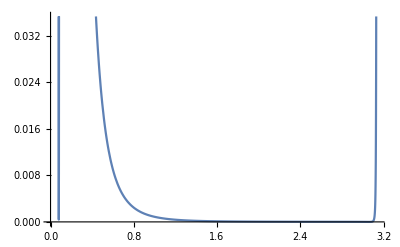

```mathematica
Plot[-result/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0},{th,0,Pi}]
```

```mathematica
-result/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0,th->0.00001}
```

8.68725×10^11

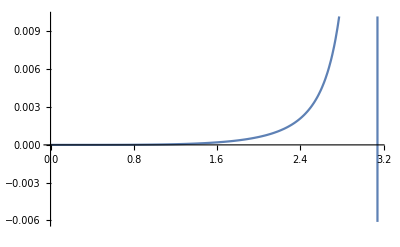

```mathematica
Plot[-result/.{MB->4.7,hi->1,hf->-1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,be->0},{th,0,Pi}]
```

```mathematica
result/.{MB->4.7,hi->1,hf->1,MH->125,MT->172,e->(13000^2-4.7^2)/26000,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1,yb->4.7/246,m->1,gs->1,yt->1,th->0}
```

1.15659×10^-41 (-3.78535×10^13 (-15625. (7.70682×10^29-1.47137×10^20 cos(be))-1.64812×10^24)+5.96857×10^17 (7.35686×10^19 cos(be)-7.70682×10^29)-2.44141×10^8 (3.65099×10^28 cos(be)-1.1395×10^-6 (1.6283×10^35 cos(be)+17.3874 (4.45938×10^20 cos(2 be)-4.45938×10^20))+6.88304×10^48)-6.23898×10^37)

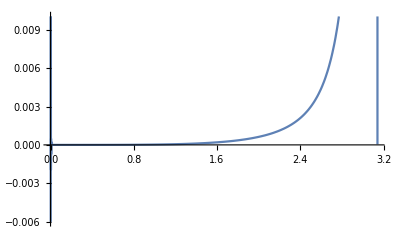

```mathematica
Plot[ampSp/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1},{th,0.,Pi}]
```

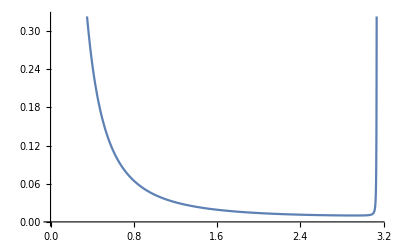

```mathematica
Plot[ampSm/.{MB->4.7,MH->125,e->(13000^2-4.7^2)/26000,hi->-1,hf->-1,ybcky->4.7/246,gs->1,ghcky->0.1/12/Pi/246,al->0,CA->1,CF->1}//FullSimplify,{th,0,Pi}]
```